## Weirstrasse M Test

If sup_(x∈S) |g_n(x)|=M_n and ∑M_n converges then f_k(x)=∑_(n=0)^k g_n(x) converges uniformly on S.

What is it? Why should I care? What is it good for?

```mathematica
TabView[{"Question"->"What is it good for?","Answer"->Style["Absolutely nothing, say it again", Struckthrough]}]
```

12

## Sums of Monomials

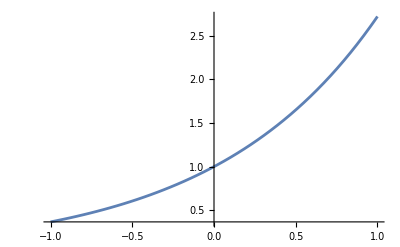

```mathematica
g[n_][x_]:= 1/(n!)x^n
f[k_][x_]:=Sum[g[n][x],{n,0,k}]
Plot[f[10][x],{x,-1,1}]
```

## Sums of Cosines

```mathematica
g[n_][x_]:= 1/(n!)Cos[n x]
f[k_][x_]:=Sum[g[n][x],{n,0,k}]
Plot[f[10][x],{x,-4,4}]
```

## Sums of Sines

```mathematica
g[n_][x_]:= If[OddQ[n],(-1)^((n-1)/2)/n^2 Sin[n x],0]
```

```mathematica
f[k_][x_]:=Sum[g[n][x],{n,0,k}]
Plot[f[34][x],{x,-4,14}]
```